# Comparação Rosane 1992

## Antonio Carlos Siqueira de Lima Paulo Eduardo Darski Rocha Hélio

## Opções de programa

```mathematica
Clear["Global`*"]
```

```mathematica
SetOptions[{ListPlot,ListLogLinearPlot,ListLogLogPlot},Axes->False,Frame->True,Joined->True,ImageSize->450,PlotStyle->{PointSize[0.015]},BaseStyle->{14,FontFamily->"Helvetica"}];
```

```mathematica
plstyle1={AbsoluteThickness[2],RGBColor[1,0,0]};
plstyle2={AbsoluteThickness[2],RGBColor[0,0,1]};
plstyle3={AbsoluteThickness[2],PointSize[.015],RGBColor[0,1,0]};
```

## Dados de Entrada

### DADOS DO PIPE TYPE

#### Cabo SC Interno

```mathematica
ncx=2 (*número de elementos metálicos*);
θjk=(2 π)/3; (*entre os cabos coaxias*)
Dsc=0.282900 10^-1; (*Distancia entre os centros dos SC's com a 1° camada da tubulação*)
μ=4.0 π 10^-7;
ϵ=8.854*10^-12;
T0=20;
```

```mathematica
(*Condutor*)
r1=0.103 10^-1;
Tc=75;
αc=0.393 10^-2;
ρc=0.172410 10^-7 (1+αc*(Tc-T0));
μc=0.999991;

(*1°Isolante*)
r2=0.116 10^-1;
r3=0.184 10^-1;
ϵc=2.6;

(*Blindagem metálica*)
r4=0.202 10^-1;
r5=0.229 10^-1;
Ts=60;
αs=0.41 10^-2;
ρs=0.2065 10^-6 (1+αs(Ts-T0));
μs=0.999983;

(*2°Isolante*)
r6=0.231 10^-1;
r7=0.245 10^-1;
ϵs=2.3;
```

#### Tubulação

```mathematica
npt=2 (*número de elementos metálicos*);
```

```mathematica
(*1°Camada PT*)
r1i=0.525 10^-1;
r1e=0.535 10^-1;
Tp1=45;
αp1=0.393 10^-2;
ρp1=0.12410 10^-7 (1+αp1(Tp1-T0));
μp1=0.999991;
ϵp1=2.6; 

(*Isolante Inter-pipes de 2 camadas*)
(*1°Camada*)
ris1i=0.536 10^-1;
ris1e=0.560 10^-1;
ϵp21=2.3; 
(*2°Camada*)
ris2i=0.560 10^-1;
ris2e=0.5845 10^-1;
ϵp22=2.6; 

(*2°Camada PT*)
r2i=0.5845 10^-1;
r2e=0.645 10^-1;
Tp2=40;
αp2=0.45 10^-2;
ρp2=0.171 10^-6 (1+αp2(Tp2-T0));
μp2=30;
ϵp2=2.6; 

(*Isolante Externo*)
ris3i=0.647 10^-1;
ris3e=0.680 10^-1;
ϵp3=2.6; 

DiametroSC=N[ris3e*2 10^3]
```

136.

### DADOS DA REDE

```mathematica
compr=10*10^3;
h=0.5;
ρg=1000;
μg=1;
```

```mathematica
ncond=3 ncx+npt(*número de elementos metálicos*)
```

8

## Configuração da Rede

### LOCALIZAÇÃO DOS CONDUTORES NO CIRCUITO DE FORÇA

#### CABOS COAXIAIS

```mathematica
xc1=0;yc1=Dsc ;
xc2=Dsc Sin[Pi/3];yc2=-Dsc Sin[Pi/6];
xc3=-Dsc  Sin[Pi/3];yc3=-Dsc Sin[Pi/6];
```

#### TUBO

```mathematica
xpt=0;
ypt=0;
```

#### LAYOUT DO PT INTERNO

```mathematica
xc={xc1,xc1,xc1,xc1,xc1,xc1,xc1,xc2,xc2,xc2,xc2,xc2,xc2,xc2,xc3,xc3,xc3,xc3,xc3,xc3,xc3,xpt,xpt,xpt,xpt,xpt,xpt,xpt,xpt,xpt,xpt};
yc={yc1,yc1,yc1,yc1,yc1,yc1,yc1,yc2,yc2,yc2,yc2,yc2,yc2,yc2,yc3,yc3,yc3,yc3,yc3,yc3,yc3,ypt,ypt,ypt,ypt,ypt,ypt,ypt,ypt,ypt,ypt};
r={r1,r2,r3,r4,r5,r6,r7,r1,r2,r3,r4,r5,r6,r7,r1,r2,r3,r4,r5,r6,r7,r1i,r1e,ris1i,ris1e,ris2i,ris2e,r2i,r2e,ris3i,ris3e};
```

```mathematica
pipe=Table[{Circle[{xc[[i]],yc[[i]]},r[[i]]]},{i,1,Length[xc]}];
```

### CABO PIPE-TYPE

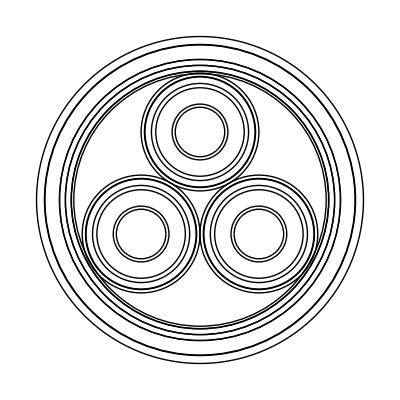

```mathematica
CaboPT=Show[Graphics[pipe],AspectRatio->Automatic,Axes->False,PlotRange->Automatic,Frame->False]
```

## Frequências e Inicialização das Listas

### Freqüências de interesse

#### Faixa de Frequência

```mathematica
d1=-1;
d2=N[6.,40];
freqlog[i_,f_,np_]:=Table[N[10^(i+x(f-i)/(Floor[np]-1))],{x,0,np-1}]
freqlin[i_,f_,np_]:=Table[N[(i+x(f-i)/(Floor[np]-1))],{x,0,np-1}]
(*f0=freqlog[d0,d1,500];*)
f1=freqlog[d1,d2,60];
f2=freqlin[10^d1, 10^d2,60];
f=Sort@Join[f2,f1];
nf=Length[f];
```

### Inicialização das listas

```mathematica
T=Table[0,{n,1,nf}];
T1=Table[0,{n,1,nf}];
λ=Table[0,{n,1,nf}];
λ0=Table[0,{n,1,nf}];
Γ1=Table[0,{n,1,nf}];
Yc1=Table[0,{n,1,nf}];
Af1=Table[0,{n,1,nf}];
Am1=Table[0,{n,1,nf}];
M1=Am1;
γm=Table[0,{n,1,nf}];
```

## Rotinas Auxiliares

### ROT

```mathematica
rot[s_?MatrixQ]:=Module[{S=s,Nc,SA,SB,scale,ang,scale1,col,scale2,err1,err2,numerator,denominator,aaa,bbb,ccc},
Nc=Length[S];
SA=Table[0,{Nc},{Nc}];
SB=SA;
scale1=Table[0,{Nc}];
scale2=scale=ang=scale1;
err1=scale1;
err2=scale1;

numerator=Table[0,{Nc}];
denominator=numerator=scale1=scale2;

For[col=1,col≤ Nc,col++,
numerator[[col]]=0.;
denominator[[col]]=numerator[[col]]=0.;

For[j=1,j≤ Nc,j++,
numerator[[col]]=numerator[[col]]+Im[S[[j,col]]]*Re[S[[j,col]]];
denominator[[col]]=denominator[[col]]+Re[S[[j,col]]]^2-Im[S[[j,col]]]^2];

numerator[[col]]=-2*numerator[[col]];
ang[[col]]=0.5*ArcTan[denominator[[col]],numerator[[col]]];
scale1[[col]]=Cos[ang[[col]]]+ⅈ*Sin[ang[[col]]];
scale2[[col]]=Cos[ang[[col]]+π/2.]+ⅈ*Sin[ang[[col]]+π/2.];

For[j=1,j≤ Nc,j++,
SA[[j,col]]=S[[j,col]]*scale1[[col]];
SB[[j,col]]=S[[j,col]]*scale2[[col]];];

aaa=0.;
bbb=0.;
ccc=0.;

For[j=1,j≤ Nc,j++,
aaa=aaa+Im[SA[[j,col]]]^2;
bbb=bbb+Re[SA[[j,col]]]*Im[SA[[j,col]]];
ccc=ccc+Re[SA[[j,col]]]^2];

err1[[col]]=aaa*Cos[ang[[col]]]^2+bbb*Sin[N[2*ang[[col]],16]]+ccc*Sin[ang[[col]]]^2;

aaa=0.;
bbb=0.;
ccc=0.;

For[j=1,j≤ Nc,j++,
aaa=aaa+Im[SB[[j,col]]]^2;
bbb=bbb+Re[SB[[j,col]]]*Im[SB[[j,col]]];
ccc=ccc+Re[SB[[j,col]]]^2];

err2[[col]]=aaa*Cos[ang[[col]]]^2+bbb*Sin[N[2*ang[[col]],16]]+ccc*Sin[ang[[col]]]^2;

If[err1[[col]]<err2[[col]],scale[[col]]=scale1[[col]],scale[[col]]=scale2[[col]]];

S[[All,col]]=S[[All,col]]*scale[[col]];
];
Return[S]
]
```

### Elimina o Cruzamento de Autovetores

```mathematica
Off[General::luc]
```

```mathematica
eigNR[G_?MatrixQ,V0_,d0_,Tol_:10^-10]:=Module[{A=G,nc,scale,v,d,vec,res,jac,i},
nc=Length[A];
scale=Norm[A];
A=A/scale;
outd=Table[0,{nc}];
outv=Table[0,{nc},{nc}];
itr=0;
jac=Table[0.0,{nc+1},{nc+1}];
Do[{v=V0[[1;;,i]];
d=d0[[i]];
res=Max[Abs[A.v-v*d]];
While[(res>Tol)&& (itr<5000),
itr=itr+1;
jac[[1;;nc,1;;nc]]=A-d*IdentityMatrix[nc];
jac[[1;;nc,nc+1]]=-v;
jac[[nc+1,1;;nc]]=2*v;
res=Join[A.v-v*d,{v.v-1}];
vec=LinearSolve[jac,res];
res=Max[Abs[vec]];
v=v-vec[[1;;nc]];
d=d-vec[[nc+1]];];
outd[[i]]=d*scale;
outv[[1;;,i]]=v;},{i,1,nc}]];
```

```mathematica
(*Tentativa de traducao direta da versao em Matlab  *)xchEig[oldT_?MatrixQ,T_?MatrixQ,d1_?ListQ]:=Module[{oldT0=oldT,T0=T,nc,ugh,ii,j,ilargest,rlargest,dotprod,dot,ind,taken,d,hjelp,ihjelp,dum,dum2,l},

nc=Length[oldT0];
dot=Table[0,{nc}];
ind=Table[0,{nc}];
taken=Table[0,{nc}];
hjelp=Table[0,{nc}];
d=DiagonalMatrix[d1];

ugh=Abs[Re[ConjugateTranspose[oldT0].T0]];


For[ii=1,ii≤nc,ii++,
ilargest=0;
rlargest=0;
For[j=1,j≤nc,j++,
dotprod=ugh[[ii,j]];
If[dotprod>rlargest,rlargest=Abs[Re[dotprod]];ilargest=j];
];
dot[[ii]]=rlargest;
ind[[ii]]=ii;
taken[[ii]]=0
];

(*sorting inner products in descending order*)
For[ii=1,ii≤ nc,ii++,
For[j=1,j≤(nc-1),j++,
If[dot[[j]]    <dot[[j+1]],
    hjelp[[1]]=dot[[j+1]];
    ihjelp         =ind[[j+1]];
    dot[[j+1]]=dot[[j]];
    ind[[j+1]]=ind[[j]];
    dot[[j]]      =hjelp[[1]];
    ind[[j]]      =ihjelp
]
]
];

(*Doing the interchange in a prioritized sequence*)
For[l=1,l≤nc,l++,
ii=ind[[l]];
ilargest=0;
rlargest=0;

For[j=1,j≤nc,j++,
If[taken[[j]]==0,dotprod=ugh[[ii,j]];
If[dotprod>rlargest,
   rlargest=Abs[Re[dotprod]];
  ilargest=j
]
]
];

taken[[ii]]=1;

hjelp=T0[[1;;,ii]];
T0[[1;;,ii]]=T0[[1;;,ilargest]];
T0[[1;;,ilargest]]=hjelp;

hjelp=d[[ii,ii]];
d[[ii,ii]]=d[[ilargest,ilargest]];
d[[ilargest,ilargest]]=hjelp;

dum=ugh[[1;;,ii]];
ugh[[1;;,ii]]=ugh[[1;;,ilargest]];
ugh[[1;;,ilargest]]=dum];


  dum2=DiagonalMatrix[Diagonal[Sign[Re[ConjugateTranspose[oldT0].T0]]]];
  
 eval=Diagonal[d];
 evect=T0  . dum2 

];
```

## Impedancia do PT

### MATRIX DE IMPEDÂNCIA INTERNA DOS CABOS (Zi)

IMPEDÂNCIAS COMPONENTES;

```mathematica
mc=√((I ω μ μc)/ρc);
ms=√((I ω μ μs)/ρs);
x1=mc r1;
x4=ms r4;
x5=ms r5;

z1=(I ω μ μc)/(2π x1)BesselI[0,x1]/BesselI[1,x1];
z2=(I ω μ)/(2π)Log[r3/r2];
z3=(I ω μ μs)/(2π x4)(BesselI[0,x4]BesselK[1,x5]+BesselK[0,x4]BesselI[1,x5])/(BesselI[1,x5]BesselK[1,x4]-BesselI[1,x4]BesselK[1,x5]);
z4=ρs/(2π r4 r5)1/(BesselI[1,x5]BesselK[1,x4]-BesselI[1,x4]BesselK[1,x5]);
z5=(I ω μ μs)/(2π x5)(BesselI[0,x5]BesselK[1,x4]+BesselK[0,x5]BesselI[1,x4])/(BesselI[1,x5]BesselK[1,x4]-BesselI[1,x4]BesselK[1,x5]);
z6=(I ω μ)/(2π)Log[r7/r6];
```

```mathematica
zcc=z1+z2+z3+z5+z6-2 z4;
zcs=z5+z6-z4;
zsc=zcs;
zss=z5+z6;
Zcc={{zcc,0,0},{0,zcc,0},{0,0,zcc}};
Zcs={{zcs,0,0},{0,zcs,0},{0,0,zcs}};
Zsc=Zcs;
Zss={{zss,0,0},{0,zss,0},{0,0,zss}};
Zero={{0,0},{0,0},{0,0}};
Zero1={{0,0},{0,0}};
Zi=ArrayFlatten[{{Zcc,Zcs,Zero},{Zsc,Zss,Zero},{Transpose[Zero],Transpose[Zero],Zero1}}];
```

```mathematica
Zi//MatrixForm;
```

### MATRIX DE IMPEDÂNCIA INTERNA DO PIPE TYPE (Zp)

FUNÇÕES AUXILIARES;

```mathematica
Dj=Dsc;
Dk=Dsc;
y1=r1i √((I ω μ μp1)/ρp1);
Cn=((Dj Dk)/r1i^2)^n  Cos[n θjk];
Qjj=Log[(r1i/r7) (1-(Dk/r1i)^2)];
Qjk=Log[r1i/(√((Dj)^2+(Dk)^2-2 Dj Dk Cos[θjk]))]-( ∑_(n=1)^12 Cn/n );
(*convergido em n=10*)
```

IMPEDÂNCIAS COMPONENTES;

```mathematica
zpp=(I ω μ)/(2 π) ((μp1 BesselK[0,y1])/(y1 BesselK[1,y1])+Qjj+2 μp1*( ∑_(n=1)^12 (Dj/r1i)^(2 n)/(n (1+μp1)+y1 BesselK[n-1,y1]/BesselK[n,y1])));
zpm=(I ω μ)/(2 π) ((μp1 BesselK[0,y1])/(y1 BesselK[1,y1])+Qjk+2 μp1*( ∑_(n=1)^12 Cn/(n (1+μp1)+y1 BesselK[n-1,y1]/BesselK[n,y1])));
```

```mathematica
Zpmt={{zpp,zpm,zpm},{zpm,zpp,zpm},{zpm,zpm,zpp}};
Zp=ArrayFlatten[{{Zpmt,Zpmt,Zero},{Zpmt,Zpmt,Zero},{Transpose[Zero],Transpose[Zero],Zero1}}];
```

```mathematica
Zp//MatrixForm;
```

### MATRIX DE IMPEDÂNCIA MÚTUA ENTRE AS SUPERFÍCIES INTERNA E EXTERNA DO PT (Zc)

```mathematica
y2=r1e √((I ω μ μp1)/ρp1);
Dp1=BesselI[1,y2]BesselK[1,y1]-BesselI[1,y1]BesselK[1,y2];
Dp2=BesselI[0,y1]BesselK[1,y2]+BesselK[0,y1]BesselI[1,y2];
Dp3=BesselI[0,y2]BesselK[1,y1]+BesselK[0,y2]BesselI[1,y1];
zpm1=ρp1/(2 π r1i r1e Dp1);
zpi1=((I ω μ μp1)/(2 π y1)) Dp2/Dp1;
zpe1=((I ω μ μp1)/(2 π y2)) Dp3/Dp1;
zis1=(I ω μ)/(2 π) Log[ris1e/ris1i]+(I ω μ)/(2 π) Log[ris2e/ris2i];


y3=r2i √((I ω μ μp2)/ρp2);
y4=r2e √((I ω μ μp2)/ρp2);
Dp4=BesselI[1,y4]BesselK[1,y3]-BesselI[1,y3]BesselK[1,y4];
Dp5=BesselI[0,y3]BesselK[1,y4]+BesselK[0,y3]BesselI[1,y4];
Dp6=BesselI[0,y4]BesselK[1,y3]+BesselK[0,y4]BesselI[1,y3];

zpm2=ρp2/(2 π r2i r2e Dp4);
zpi2=((I ω μ μp2)/(2 π y3)) Dp5/Dp4;
zpe2=((I ω μ μp2)/(2 π y4)) Dp6/Dp4;
zis2=(I ω μ)/(2 π) Log[ris3e/ris3i];
```

```mathematica
zc1=zpi1+zpe1-2 zpm1+zis1 +zpi2+zpe2-2 zpm2 + zis2;
zc2=zpe1-zpm1+zis1 +zpi2+zpe2-2 zpm2 + zis2;
zc3=zpe1+zis1 +zpi2+zpe2-2 zpm2 + zis2;
zc4=zpe2-zpm2 + zis2;
zc5=zpe2 + zis2;
```

#### MATRIX Zc

```mathematica
Zc={{zc1,zc1,zc1,zc1,zc1,zc1,zc2,zc4},
{zc1,zc1,zc1,zc1,zc1,zc1,zc2,zc4},
{zc1,zc1,zc1,zc1,zc1,zc1,zc2,zc4},
{zc1,zc1,zc1,zc1,zc1,zc1,zc2,zc4},
{zc1,zc1,zc1,zc1,zc1,zc1,zc2,zc4},
{zc1,zc1,zc1,zc1,zc1,zc1,zc2,zc4},
{zc2,zc2,zc2,zc2,zc2,zc2,zc3,zc4},
{zc4,zc4,zc4,zc4,zc4,zc4,zc4,zc5}};
Zc//MatrixForm;
```

## Matriz P do PT

### MATRIX DO COEFICIENTE DE POTENCIAL INTERNO DOS CABOS (Pi)

#### MATRIX DE POTENCIAL INTERNO DO CABO COAXIAL

FUNÇÕES AUXILIARES;

```mathematica
pc=1/(2 π ϵ ϵc) Log[r2/r1];
ps=1/(2 π ϵ ϵs) Log[r4/r3];
p1coaxial={{pc+ps,ps},{ps,ps}};
p3coaxial=ArrayFlatten[{{p1coaxial,0,0},{0,p1coaxial,0},{0,0,p1coaxial}}];
p3coaxial//MatrixForm
```

(1.55119×10^9 | 7.29429×10^8 | 0 | 0 | 0 | 0
7.29429×10^8 | 7.29429×10^8 | 0 | 0 | 0 | 0
0 | 0 | 1.55119×10^9 | 7.29429×10^8 | 0 | 0
0 | 0 | 7.29429×10^8 | 7.29429×10^8 | 0 | 0
0 | 0 | 0 | 0 | 1.55119×10^9 | 7.29429×10^8
0 | 0 | 0 | 0 | 7.29429×10^8 | 7.29429×10^8)

```mathematica
(*y3coaxial=s Inverse[p3coaxial];
y3coaxial//MatrixForm*)
```

#### MATRIX Pi

MONTAGEM;

```mathematica
Pii=ArrayFlatten[{{p3coaxial,0,0},{0,0,0},{0,0,0}}];
Pii//MatrixForm
```

(1.55119×10^9 | 7.29429×10^8 | 0 | 0 | 0 | 0 | 0 | 0
7.29429×10^8 | 7.29429×10^8 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1.55119×10^9 | 7.29429×10^8 | 0 | 0 | 0 | 0
0 | 0 | 7.29429×10^8 | 7.29429×10^8 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1.55119×10^9 | 7.29429×10^8 | 0 | 0
0 | 0 | 0 | 0 | 7.29429×10^8 | 7.29429×10^8 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

### MATRIX DO COEFICIENTE DE POTENCIAL INTERNO DO PIPE TYPE (Pp)

#### CABOS COAXIAIS

POTENCIAIS;

```mathematica
ppcx=Qjj/(2 π ϵ ϵp1);
pmcx=Qjk/(2 π ϵ ϵp1);
```

```mathematica
ppcoaxial=ArrayFlatten[{{Table[ppcx,{i,1,ncx},{j,1,ncx}],Table[pmcx,{i,1,ncx},{j,1,ncx}],Table[pmcx,{i,1,ncx},{j,1,ncx}]},{Table[pmcx,{i,1,ncx},{j,1,ncx}],Table[ppcx,{i,1,ncx},{j,1,ncx}],Table[pmcx,{i,1,ncx},{j,1,ncx}]},{Table[pmcx,{i,1,ncx},{j,1,ncx}],Table[pmcx,{i,1,ncx},{j,1,ncx}],Table[ppcx,{i,1,ncx},{j,1,ncx}]}}];
ppcoaxial//MatrixForm
```

(2.89774×10^9 | 2.89774×10^9 | 1.57707×10^9 | 1.57707×10^9 | 1.57707×10^9 | 1.57707×10^9
2.89774×10^9 | 2.89774×10^9 | 1.57707×10^9 | 1.57707×10^9 | 1.57707×10^9 | 1.57707×10^9
1.57707×10^9 | 1.57707×10^9 | 2.89774×10^9 | 2.89774×10^9 | 1.57707×10^9 | 1.57707×10^9
1.57707×10^9 | 1.57707×10^9 | 2.89774×10^9 | 2.89774×10^9 | 1.57707×10^9 | 1.57707×10^9
1.57707×10^9 | 1.57707×10^9 | 1.57707×10^9 | 1.57707×10^9 | 2.89774×10^9 | 2.89774×10^9
1.57707×10^9 | 1.57707×10^9 | 1.57707×10^9 | 1.57707×10^9 | 2.89774×10^9 | 2.89774×10^9)

#### MATRIX Pp

MONTAGEM;

```mathematica
Pp=ArrayFlatten[{{ppcoaxial,0,0},{0,0,0},{0,0,0}}];
```

```mathematica
Pp//MatrixForm
```

(2.89774×10^9 | 2.89774×10^9 | 1.57707×10^9 | 1.57707×10^9 | 1.57707×10^9 | 1.57707×10^9 | 0 | 0
2.89774×10^9 | 2.89774×10^9 | 1.57707×10^9 | 1.57707×10^9 | 1.57707×10^9 | 1.57707×10^9 | 0 | 0
1.57707×10^9 | 1.57707×10^9 | 2.89774×10^9 | 2.89774×10^9 | 1.57707×10^9 | 1.57707×10^9 | 0 | 0
1.57707×10^9 | 1.57707×10^9 | 2.89774×10^9 | 2.89774×10^9 | 1.57707×10^9 | 1.57707×10^9 | 0 | 0
1.57707×10^9 | 1.57707×10^9 | 1.57707×10^9 | 1.57707×10^9 | 2.89774×10^9 | 2.89774×10^9 | 0 | 0
1.57707×10^9 | 1.57707×10^9 | 1.57707×10^9 | 1.57707×10^9 | 2.89774×10^9 | 2.89774×10^9 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

### MATRIX DO COEFICIENTE DE POTENCIAL ENTRE AS SUPERFÍCIES INTERNA E EXTERNA DO PT (Pc)

#### CÁLCULO DE Pc

```mathematica
Pc1=(1/(2 π ϵ ϵp21) Log[ris1e/ris1i]+1/(2 π ϵ ϵp22) Log[ris2e/ris2i]+1/(2 π ϵ ϵp3) Log[ris3e/ris3i]);
Pc2=Pc1;
Pc3=Pc2;
Pc4=1/(2 π ϵ ϵp3) Log[ris3e/ris3i];
Pc5=Pc4;
```

#### MATRIX Pc

```mathematica
Pc=ArrayFlatten[{{Table[Pc1, {i,1,3( ncx)}, {j,1,3( ncx)}],Table[Pc2, {i,1,3( ncx)}, {j,1,1}],Table[Pc4, {i,1,3( ncx)}, {j,1,1}]},{Transpose[Table[Pc2, {i,1,3( ncx)}, {j,1,1}]],Pc3,Pc4},{Transpose[Table[Pc4, {i,1,3( ncx)}, {j,1,1}]],Pc4,Pc5}}];
Pc//MatrixForm
```

(9.82308×10^8 | 9.82308×10^8 | 9.82308×10^8 | 9.82308×10^8 | 9.82308×10^8 | 9.82308×10^8 | 9.82308×10^8 | 3.4393×10^8
9.82308×10^8 | 9.82308×10^8 | 9.82308×10^8 | 9.82308×10^8 | 9.82308×10^8 | 9.82308×10^8 | 9.82308×10^8 | 3.4393×10^8
9.82308×10^8 | 9.82308×10^8 | 9.82308×10^8 | 9.82308×10^8 | 9.82308×10^8 | 9.82308×10^8 | 9.82308×10^8 | 3.4393×10^8
9.82308×10^8 | 9.82308×10^8 | 9.82308×10^8 | 9.82308×10^8 | 9.82308×10^8 | 9.82308×10^8 | 9.82308×10^8 | 3.4393×10^8
9.82308×10^8 | 9.82308×10^8 | 9.82308×10^8 | 9.82308×10^8 | 9.82308×10^8 | 9.82308×10^8 | 9.82308×10^8 | 3.4393×10^8
9.82308×10^8 | 9.82308×10^8 | 9.82308×10^8 | 9.82308×10^8 | 9.82308×10^8 | 9.82308×10^8 | 9.82308×10^8 | 3.4393×10^8
9.82308×10^8 | 9.82308×10^8 | 9.82308×10^8 | 9.82308×10^8 | 9.82308×10^8 | 9.82308×10^8 | 9.82308×10^8 | 3.4393×10^8
3.4393×10^8 | 3.4393×10^8 | 3.4393×10^8 | 3.4393×10^8 | 3.4393×10^8 | 3.4393×10^8 | 3.4393×10^8 | 3.4393×10^8)

```mathematica
Pc//Dimensions
```

{8,8}

### MATRIX P DO PT INTERNO

```mathematica
Ppipe=Pii+Pp+Pc;
Ppipe//MatrixForm
```

(5.43124×10^9 | 4.60947×10^9 | 2.55937×10^9 | 2.55937×10^9 | 2.55937×10^9 | 2.55937×10^9 | 9.82308×10^8 | 3.4393×10^8
4.60947×10^9 | 4.60947×10^9 | 2.55937×10^9 | 2.55937×10^9 | 2.55937×10^9 | 2.55937×10^9 | 9.82308×10^8 | 3.4393×10^8
2.55937×10^9 | 2.55937×10^9 | 5.43124×10^9 | 4.60947×10^9 | 2.55937×10^9 | 2.55937×10^9 | 9.82308×10^8 | 3.4393×10^8
2.55937×10^9 | 2.55937×10^9 | 4.60947×10^9 | 4.60947×10^9 | 2.55937×10^9 | 2.55937×10^9 | 9.82308×10^8 | 3.4393×10^8
2.55937×10^9 | 2.55937×10^9 | 2.55937×10^9 | 2.55937×10^9 | 5.43124×10^9 | 4.60947×10^9 | 9.82308×10^8 | 3.4393×10^8
2.55937×10^9 | 2.55937×10^9 | 2.55937×10^9 | 2.55937×10^9 | 4.60947×10^9 | 4.60947×10^9 | 9.82308×10^8 | 3.4393×10^8
9.82308×10^8 | 9.82308×10^8 | 9.82308×10^8 | 9.82308×10^8 | 9.82308×10^8 | 9.82308×10^8 | 9.82308×10^8 | 3.4393×10^8
3.4393×10^8 | 3.4393×10^8 | 3.4393×10^8 | 3.4393×10^8 | 3.4393×10^8 | 3.4393×10^8 | 3.4393×10^8 | 3.4393×10^8)

```mathematica
Ypipe=I ω  Inverse[Ppipe];
Ypipe//MatrixForm
```

(1.21689×10^-9 ⅈ ω | -1.21689×10^-9 ⅈ ω | -1.57996×10^-43 ⅈ ω | -4.09296×10^-27 ⅈ ω | -5.3153×10^-43 ⅈ ω | -4.09296×10^-27 ⅈ ω | 5.57571×10^-26 ⅈ ω | -4.34782×10^-26 ⅈ ω
-1.21689×10^-9 ⅈ ω | 1.59124×10^-9 ⅈ ω | -1.84483×10^-26 ⅈ ω | -1.13439×10^-10 ⅈ ω | 1.52929×10^-26 ⅈ ω | -1.13439×10^-10 ⅈ ω | -1.47464×10^-10 ⅈ ω | 0. ⅈ ω
6.4878×10^-30 ⅈ ω | 6.61079×10^-27 ⅈ ω | 1.21689×10^-9 ⅈ ω | -1.21689×10^-9 ⅈ ω | -2.43152×10^-42 ⅈ ω | -2.28267×10^-26 ⅈ ω | 4.6934×10^-26 ⅈ ω | -5.2784×10^-26 ⅈ ω
-6.27308×10^-27 ⅈ ω | -1.13439×10^-10 ⅈ ω | -1.21689×10^-9 ⅈ ω | 1.59124×10^-9 ⅈ ω | -1.94818×10^-26 ⅈ ω | -1.13439×10^-10 ⅈ ω | -1.47464×10^-10 ⅈ ω | 3.10449×10^-26 ⅈ ω
1.67312×10^-26 ⅈ ω | -2.75396×10^-27 ⅈ ω | -1.18271×10^-29 ⅈ ω | -2.7771×10^-27 ⅈ ω | 1.21689×10^-9 ⅈ ω | -1.21689×10^-9 ⅈ ω | 1.7009×10^-26 ⅈ ω | 9.30576×10^-27 ⅈ ω
-6.229×10^-26 ⅈ ω | -1.13439×10^-10 ⅈ ω | 3.47802×10^-26 ⅈ ω | -1.13439×10^-10 ⅈ ω | -1.21689×10^-9 ⅈ ω | 1.59124×10^-9 ⅈ ω | -1.47464×10^-10 ⅈ ω | -3.10449×10^-26 ⅈ ω
2.54045×10^-25 ⅈ ω | -1.47464×10^-10 ⅈ ω | -5.69242×10^-27 ⅈ ω | -1.47464×10^-10 ⅈ ω | -1.91504×10^-26 ⅈ ω | -1.47464×10^-10 ⅈ ω | 2.00886×10^-9 ⅈ ω | -1.56647×10^-9 ⅈ ω
-1.65901×10^-25 ⅈ ω | 1.8814×10^-25 ⅈ ω | 4.45549×10^-26 ⅈ ω | -6.77284×10^-26 ⅈ ω | 9.93334×10^-27 ⅈ ω | -5.15095×10^-26 ⅈ ω | -1.56647×10^-9 ⅈ ω | 4.47404×10^-9 ⅈ ω)

## Rotinas Auxiliares

## Rotina

```mathematica
AbsoluteTiming[Do[{ω=2 π f[[nm]],
(*Retorno pelo solo*)
mg=√((I ω μ μg)/ρg),
de=√(ris3e^2+(2h)^2),
polchk=2 NIntegrate[Exp[-2 h √((α^2)+mg^2)]/(α+√((α^2)+mg^2))Cos[ris3e α],{α,0,∞},MaxRecursion->50],
zs=ⅉ(ω μ)/(2π)(BesselK[0,mg ris3e]-BesselK[0,mg  de]+polchk),
Z0=Table[zs,{i,1,8},{j,1,8}],
(*Matriz Z*)
Zcabo=Zi+Zp+Zc+Z0,
Ycabo=Ypipe,
Γ= Ycabo.Zcabo,
nc=Length[Zcabo];
k=nm,

If[k==1,
{eval,evec}=Eigensystem[Γ];
 evelho=rot[Transpose[evec]],
eigNR[Γ,evelho,eval];
eval=outd;
evelho=outv;
],
λ0[[nm]]=Sqrt[eval];
Am1[[nm]]=Exp[-λ0[[nm]] compr],
T[[nm]]=evelho

},
{nm,1,nf}]]
```

{73.7195632,Null}

### Descruzamento de Autovetores

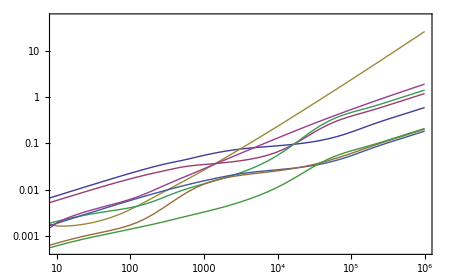

```mathematica
ListLogLogPlot[{Transpose@{f,1000 Re[λ0[[All,1]]]},
Transpose@{f,1000 Re[λ0[[All,2]]]},
Transpose@{f,1000 Re[λ0[[All,3]]]},
Transpose@{f,1000 Re[λ0[[All,4]]]},
Transpose@{f,1000 Re[λ0[[All,5]]]},
Transpose@{f,1000 Re[λ0[[All,6]]]},
Transpose@{f,1000 Re[λ0[[All,7]]]},
Transpose@{f,1000 Re[λ0[[All,8]]]}
},PlotRange->{{10,1000000},{.5 10^-3,50}}]
```

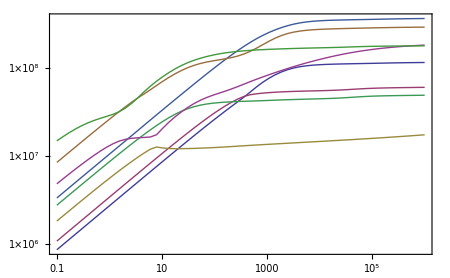

```mathematica
ListLogLogPlot[{Transpose@{f,2 π f/Im[λ0[[All,1]]]},
Transpose@{f,2 π f/Im[λ0[[All,2]]]},
Transpose@{f,2 π f/Im[λ0[[All,3]]]},
Transpose@{f,2 π f/Im[λ0[[All,4]]]},
Transpose@{f,2 π f/Im[λ0[[All,5]]]},
Transpose@{f,2 π f/Im[λ0[[All,6]]]},
Transpose@{f,2 π f/Im[λ0[[All,7]]]},
Transpose@{f,2 π f/Im[λ0[[All,8]]]}
},PlotRange-> All]
```

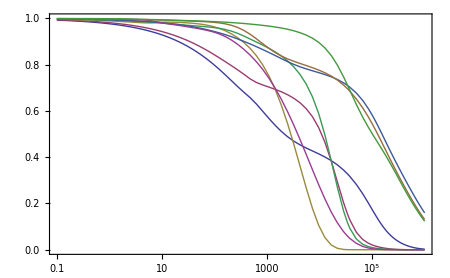

```mathematica
ListLogLinearPlot[{Transpose@{f,Abs[Am1[[All,1]]]},
Transpose@{f,Abs[Am1[[All,2]]]},
Transpose@{f,Abs[Am1[[All,3]]]},
Transpose@{f,Abs[Am1[[All,4]]]},
Transpose@{f,Abs[Am1[[All,5]]]},
Transpose@{f,Abs[Am1[[All,6]]]},
Transpose@{f,Abs[Am1[[All,7]]]},
Transpose@{f,Abs[Am1[[All,8]]]}
},PlotRange-> All]
```